```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\GitHub\VM2D\settings\airfoils

```mathematica
n=200;
```

```mathematica
Pts=N[Table[N[1/2{Cos[(2π)/n(i-1.0)],Sin[(2π)/n(i-1.0)]}],{i,1,n}],16];
```

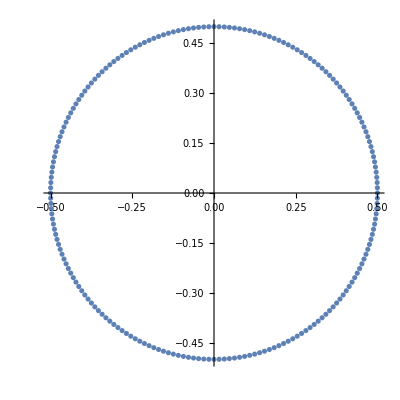

```mathematica
ListPlot[Pts,AspectRatio->Automatic]
```

```mathematica
Export["circle"<>ToString[n],
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.5    |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2019/02/20     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2019 Ilia Marchevsky, Kseniia Kuzmina, Evgeniya Ryatina  |
*-----------------------------------------------------------------------------*
| File name: circle"<>ToString[n]<>StringRepeat[" ",59-StringLength@ToString[n]]<>"|
| Info: Circular airfoil ("<>ToString[n]<>" panels)"<>StringRepeat[" ",44-StringLength@ToString[n]]<>"|
\\*---------------------------------------------------------------------------*/
"}~Join~{"r = {"}~Join~((ToString[SetPrecision[#,17]]<>",")&/@(Pts[[1;;-2]]))~Join~((ToString[SetPrecision[#,17]])&/@(Pts[[{-1}]]))~Join~{" };"},"Table"]
```

circle200